```mathematica
A = {{0,1},{1,0}};
B = {{1,0},{1,1}};
{MatrixForm[A],MatrixForm[B]}
```

{(0 | 1
1 | 0),(1 | 0
1 | 1)}

```mathematica
I2 = IdentityMatrix[2];
```

```mathematica
Q = (A - x I2) . (A - x I2)+ ConjugateTranspose[(B - (y + ⅈ z) I2)] .  (B - (y + ⅈ z) I2) ;
Q = FullSimplify[Q,x∈Reals && y∈Reals&& z∈Reals];
```

```mathematica
MatrixForm[Q]
```

(3+x^2+(-2+y) y+z^2 | 1-2 x-y-ⅈ z
1-2 x-y+ⅈ z | 2+x^2+(-2+y) y+z^2)

```mathematica
{evalQ,evecQ} = Eigensystem[Q]
```

{{1/2 (5+2 x^2-4 y+2 y^2+2 z^2-√(5-16 x+16 x^2-8 y+16 x y+4 y^2+4 z^2)),1/2 (5+2 x^2-4 y+2 y^2+2 z^2+√(5-16 x+16 x^2-8 y+16 x y+4 y^2+4 z^2))},{{-(1-√(5-16 x+16 x^2-8 y+16 x y+4 y^2+4 z^2))/(2 (-1+2 x+y-ⅈ z)),1},{-(1+√(5-16 x+16 x^2-8 y+16 x y+4 y^2+4 z^2))/(2 (-1+2 x+y-ⅈ z)),1}}}

```mathematica
sMin = Simplify[evalQ[[1]],x∈Reals && y∈Reals&& z∈Reals]
```

5/2+x^2-2 y+y^2+z^2-1/2 √(5+16 x^2+16 x (-1+y)-8 y+4 y^2+4 z^2)

```mathematica
DzsMin = Together[D[sMin,z]]
```

(2 z (-1+√(5-16 x+16 x^2-8 y+16 x y+4 y^2+4 z^2)))/(√(5-16 x+16 x^2-8 y+16 x y+4 y^2+4 z^2))

```mathematica
Simplify[Expand[(4x +2 y -2)^2+4 z^2 +1]]
```

5+16 x^2+16 x (-1+y)-8 y+4 y^2+4 z^2

```mathematica
Q = ReplaceAll[Q,z->0]
```

{{3+x^2+(-2+y) y,1-2 x-y},{1-2 x-y,2+x^2+(-2+y) y}}

```mathematica
{evalQ,evecQ} = Simplify[Eigensystem[Q],x∈Reals && y∈Reals&& z∈Reals]
```

{{5/2+x^2-2 y+y^2-1/2 √(5+16 x^2+16 x (-1+y)-8 y+4 y^2),5/2+x^2-2 y+y^2+1/2 √(5+16 x^2+16 x (-1+y)-8 y+4 y^2)},{{(-1+√(5+16 x^2+16 x (-1+y)-8 y+4 y^2))/(2 (-1+2 x+y)),1},{-(1+√(5+16 x^2+16 x (-1+y)-8 y+4 y^2))/(2 (-1+2 x+y)),1}}}

```mathematica
sMin = ReplaceAll[sMin,z->0]
```

5/2+x^2-2 y+y^2-1/2 √(5+16 x^2+16 x (-1+y)-8 y+4 y^2)

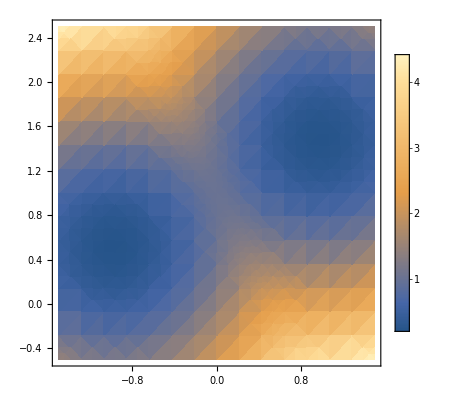

```mathematica
DensityPlot[ sMin,{x,-1.5,1.5},{y,-0.5,2.5},PlotLegends->True]
```

```mathematica
minOnGraph = Minimize[{sMin,x>0},{x,y}]
```

{1/5,{x→(2 √6)/5,y→1/5 (5+√6)}}

```mathematica
minOnGraph = Minimize[{sMin,x<0},{x,y}]
```

{1/5,{x→-(2 √6)/5,y→1/5 (5-√6)}}

```mathematica
Qmin = ReplaceAll[Q,minOnGraph[[2]]];
```

```mathematica
MatrixForm[Qmin]
```

(99/25+1/5 (5-√6) (-2+1/5 (5-√6)) | 1+(4 √6)/5+1/5 (-5+√6)
1+(4 √6)/5+1/5 (-5+√6) | 74/25+1/5 (5-√6) (-2+1/5 (5-√6)))

```mathematica
{sMin,vec} = Eigensystem[Qmin]
```

{{26/5,1/5},{{√(3/2),1},{-√(2/3),1}}}

```mathematica
sMin = sMin[[2]]
```

1/5

```mathematica
vec = vec[[2]]
```

{-√(2/3),1}

```mathematica
N[sMin]
```

0.2

```mathematica
Simplify[(1/Norm[vec]) vec]
```

{-√(2/5),√(3/5)}